# Simulated Multiple-Scattering Fresnel Factor

The idea here is to use my MSBRDF simulator to cast many rays on a tiny surface and measure the total energy that comes out for several scattering orders (up to 6, the 7th order stores the total of the remaining 6+ orders).

I ran the simulation for 16 incidence angles from 0 to 90°, 16 surface roughness values and 20 F_0 values from 1 (IOR=∞) down to 0.04 (IOR= 1.5, the classical dielectric value used in many 3D engines).

Theoretically, total energy for order 1 should be roughly the energy of a Cook-Torrance BRDF (because my simulator uses a heightfield with a Beckmann distribution of heights, not a GGX distribution)(using the code from Heitz).
The sum of the energy output by all other orders should be equivalent to our magical multiple-scattering term:

	π-E_avg(α)=π-∫E_o(θ_o,α) cos(θ_o) ⅆ θ_o

The goal then is to check that it is indeed the case.
Then, we must decompose the numerical simulation of orders 2+ to understand what are their general shape (if any can be found, but an approximation will suffice) and what law governs the dependence on F_0, typically we expect order 1 to be directly linked to F_0 while order 2 should be linked to F_0^2 and subsequent order N to F_0^N.

Eventually, we’re looking for some expression that would look like this:

	E_avg^j(θ_i,α,F_0)= f(θ_i,α)·g(j)·(h(F_0))^j

f(θ_i,α) is some general expression we don’t really care about since the ∑_(j=2)^∞ E_avg^j(θ_i,α,F_0=1)=π-E_avg(α)
g(j) is some amplitude function depending on the order j
h(F_0) is some mapping from F_0 to an expression that can be raised to the power of the current order

```mathematica
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 
countTheta = 16;
countRoughness= 16;
countF0=20;
countOrders=7;
taRawTotalReflectances=Table[
Import["TotalReflectance_"  <>ToString[countTheta] <>"x"  <>ToString[countRoughness] <>"x"  <>ToString[countF0] <>"_order"  <>ToString[order] <>".bin", "Real64"],{order,1,countOrders}];
```

Generate list interpolations

```mathematica
fTotalReflectance=Table[
ListInterpolation[Table[
taRawTotalReflectances[[order]][[countTheta*((roughness-1)+countRoughness*(albedo-1))+theta]],{theta,1,countTheta},{roughness,1,countRoughness},{albedo,1,countF0}],{{0,π/2},{1,0},{1,0.04}}],
{order,1,countOrders}];
```

```mathematica
Manipulate[
Plot3D[fTotalReflectance[[order]][x,α,ρ],{x,0,π/2},{α,0,1},PlotRange->{0,3^(-order+1)}],{{ρ,1},0.04,1},{{order,2},1,countOrders,1}]
```

## Show Total Reflectance Depending on F_0

```mathematica
Manipulate[Plot3D[Sum[fTotalReflectance[[order]][x,α,ρ],{order,1,countOrders}],{x,0,π/2},{α,0,1},PlotRange->{0,1},AxesLabel->{"θ","α"}],{{ρ,1},0.04,1}]
```

```mathematica
Manipulate[Plot3D[Sum[fTotalReflectance[[order]][x,α,ρ],{order,2,countOrders}],{x,0,π/2},{α,0,1},PlotRange->{0,0.3},AxesLabel->{"θ","α"}],{{ρ,1},0.04,1}]
```

Visualizing each individual order

```mathematica
Manipulate[
Show[
Table[
Plot3D[fTotalReflectance[[order]][x,α,ρ],{x,0,π/2},{α,0,1},
PlotRange->{0,0.4},PlotStyle->Hue[(4*(order-2))/countOrders]],{order,2,countOrders}]
],
{{ρ,1},0.04,1}]
```

## White Furnace Comparison

```mathematica
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 
countX=128;
countY=128;
resultEo = Import["MSBRDF_E128x128.csv","CSV"];
resultEavg=Import["MSBRDF_Eavg128.csv","CSV"];
fEo=ListInterpolation[Table[resultEo[[1+countX*(y-1)+(x-1)]][[3]],{x,1,countY},{y,1,countY}],{{0,1},{0,1}}]
fEavg=ListInterpolation[Table[resultEavg[[i]][[2]],{i,1,countY}],{0,1}]
Plot[fEavg[x],{x,0,1},PlotRange->{0,π}, AxesLabel->{"α","E_avg"}];
Plot3D[fEo[x,y],{x,0,1},{y,0,1},AxesLabel->{"cos(θ)", "α","E_i"}];

BRDFggx[θo_,θi_,ϕi_,α_]:= smith[θo,α]*smith[θi,α]*ggx[change[θo,θi,ϕi],α]
BRDFms[θo_,θi_,α_]:=((1-fEo[Cos[θo],α])*(1-fEo[Cos[θi],α]))/(π-fEavg[α])
fWhiteFurnaceSS[α_]:=2*π*NIntegrate[BRDFggx[θo,θi,ϕi,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
fWhiteFurnaceMS[α_]:=2*π*NIntegrate[BRDFms[θo,θi,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
fWhiteFurnaceSS[0.3]
fWhiteFurnaceMS[0.3]
π-fEavg[0.3]
fWhiteFurnaceSS[0.3]+fWhiteFurnaceMS[0.3]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

InterpolatingFunction[{{0., 1.}}, <>]

NIntegrate::inumr: The integrand Cos[θi]\ Cos[θo]\ ggx[change[θo, θi, ϕi], 0.3]\ Sin[θi]\ Sin[θo]\ smith[θi, 0.3]\ smith[θo, 0.3] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1.5708}, {-3.14159, 3.14159}, {0, 1.5708}}.

2 π NIntegrate[BRDFggx[θo,θi,ϕi,0.3] Cos[θi] Sin[θi] Cos[θo] Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision→MachinePrecision]

0.493886

0.493886

NIntegrate::inumr: The integrand Cos[θi]\ Cos[θo]\ ggx[change[θo, θi, ϕi], 0.3]\ Sin[θi]\ Sin[θo]\ smith[θi, 0.3]\ smith[θo, 0.3] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1.5708}, {-3.14159, 3.14159}, {0, 1.5708}}.

0.493886+2 π NIntegrate[BRDFggx[θo,θi,ϕi,0.3] Cos[θi] Sin[θi] Cos[θo] Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision→MachinePrecision]

```mathematica
whiteFurnaceMS=Table[{α,π-fEavg[α]},{α,0,1,0.05}]
```

{{0.,0.00161736},{0.05,0.0277751},{0.1,0.0893483},{0.15,0.172407},{0.2,0.270382},{0.25,0.378701},{0.3,0.493886},{0.35,0.613187},{0.4,0.734396},{0.45,0.855729},{0.5,0.97577},{0.55,1.0934},{0.6,1.20774},{0.65,1.31816},{0.7,1.42419},{0.75,1.52552},{0.8,1.62196},{0.85,1.71343},{0.9,1.79993},{0.95,1.88154},{1.,1.95836}}

Here we show that we mustn’t forget that the MS white furnace amounts to the complement of the total energy lost by SS BRDF...

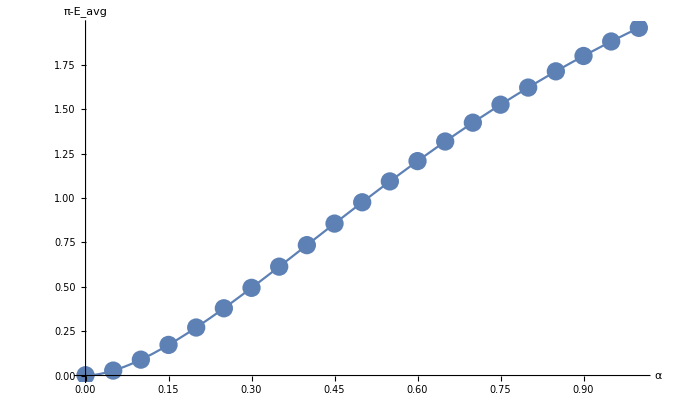

```mathematica
Show[ListPlot[whiteFurnaceMS,PlotRange->Full, AxesLabel->{"α","π-E_avg"}],
Plot[π-fEavg[x],{x,0,1}]
]
```

Comparing with Simulation

We computed the total energy bouncing off the surface at various scattering orders for different values of roughness, incidence angle and albedos.
So basically we performed:

	E(ω_i,α,ρ)=∫_(Ω^+) L_i(ω_i) f_r( ω_o,ω_i,α,ρ)(ω_o·n)dω_o
	
With L_i(ω_i)=1
To compute the equivalent white furnace test we thus need to compute:

	E_total(α,ρ)=∫_(Ω^+) E(ω_i,α,ρ)(ω_i·n)dω_i

```mathematica
taRawSumTotalReflectances=Sum[taRawTotalReflectances[[order]],{order,2,countOrders}]; (* Sum all orders > 2 *)
MSTotalReflectances=ListInterpolation[Table[taRawSumTotalReflectances[[countTheta*((roughness-1)+countRoughness*(F0-1))+theta]],{theta,1,countTheta},{roughness,1,countRoughness},{F0,1,countF0}],{{0,π/2},{1,0},{1,0.04}}]
fWhiteFurnaceSimul[α_,ρ_,order_]:=2*π*NIntegrate[fTotalReflectance[[order]][θi,α,ρ]*Cos[θi]*Sin[θi],{θi,0,π/2},WorkingPrecision->MachinePrecision];
fSumWhiteFurnaceSimul[α_,ρ_]:=2*π*NIntegrate[MSTotalReflectances[θi,α,ρ]*Cos[θi]*Sin[θi],{θi,0,π/2},WorkingPrecision->MachinePrecision];
```

InterpolatingFunction[{{0., 1.5708}, {0., 1.}, {0.04, 1.}}, <>]

```mathematica
Plot3D[fSumWhiteFurnaceSimul[α,ρ],{α,0,1},{ρ,0.04,1},PlotRange->{0,1},AxesLabel->{"α","ρ"}]
```

-Graphics3D-

Here we show that the white furnace tests for the simulated data also complement to π

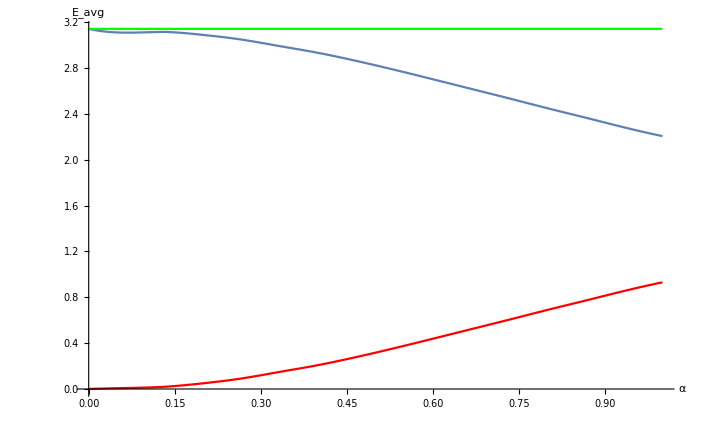

```mathematica
ρ=1;
Show[
Plot[fWhiteFurnaceSimul[α,ρ,1],{α,0,1},PlotRange->{0,π},AxesLabel->{"α","E_avg"}]
,Plot[fSumWhiteFurnaceSimul[α,ρ],{α,0,1},PlotRange->Full,PlotStyle->Red]
,Plot[π,{α,0,1},PlotRange->Full,PlotStyle->Green]
]
```

2.10521

Union::normal: Nonatomic expression expected at position 1 in Union[whiteFurnaceResult1].

ListLinePlot::lpn: whiteFurnaceResult1 is not a list of numbers or pairs of numbers.

Union::normal: Nonatomic expression expected at position 1 in Union[whiteFurnaceResult1].

ListLinePlot::lpn: whiteFurnaceResult1 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ListLinePlot[whiteFurnaceResult1, AxesLabel → {.

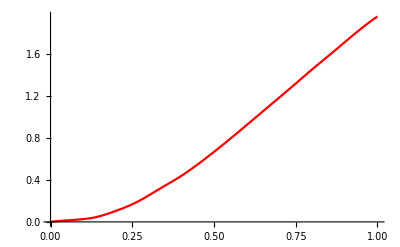
Show[ListLinePlot[whiteFurnaceResult1,AxesLabel→{α,E_avg}],-Graphics-]

```mathematica
factor=(π-fEavg[1])/fSumWhiteFurnaceSimul[1,1]
Show[
ListLinePlot[whiteFurnaceResult1,AxesLabel->{"α","E_avg"}]
,Plot[factor*fSumWhiteFurnaceSimul[α,ρ],{α,0,1},PlotStyle->Red]
]
```

We see here the red curve is not quite the same as the white furnace result given by the theoretical multiple-scattering expression for the GGX BRDF. The global factor 2.1 is quite worrying but otherwise, the difference in shape is certainly due to the GGX distribution of normals that is not the same as the Beckmann distribution I used in the simulation.
Overall, we won’t linger too much on these differences and assume the simulation represents ground-truth data.
We are more interested in the relative behavior of individual orders one to another and the geometric progression that is expected from varying the F_0 term.

## Finding an Analytical Model

We saw that integrating our order 2^+ irradiance values (the red curve in the above graph) yields π-E_total where E_total(α,ρ) is the total irradiance reflected for the single-scattering Cook-Torrance BRDF (NOT GGX BRDF, because I don’t know how to generate a simulation height field with a Smith distribution of heights) (I should re-read Heitz papers but I remember it’s quite complicated, I’m not even sure he provided the code for that).

We are interested in how each order contributes to that complement.
We assume the roughness-dependent shape is not important (i.e. it’s computed by the analytical E_avg expression for the GGX MSBRDF) and concentrate on the maximum values of the white furnace functions for each order, when α=1.
But we are interested in the evolution of that maximum value when varying the albedo!

So let’s create a table of samples of white furnace values for varying albedos, for each order (except last order, which is a compound of all remaining orders and doesn’t interest us):

```mathematica
α=1;
taWhiteFurnace=
Table[fWhiteFurnaceSimul[α,ρ,order],{order,2,countOrders},{ρ,0.04,1,0.02}];
```

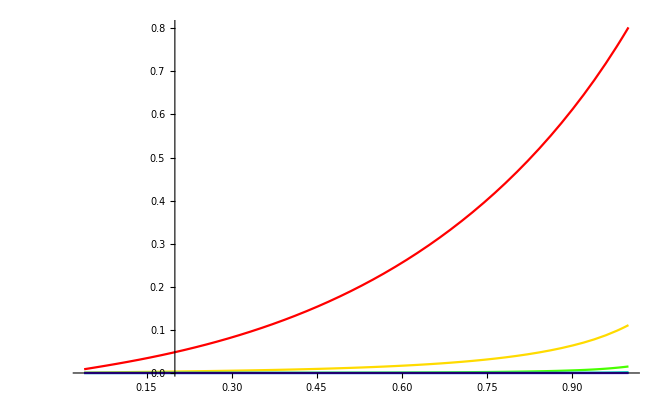

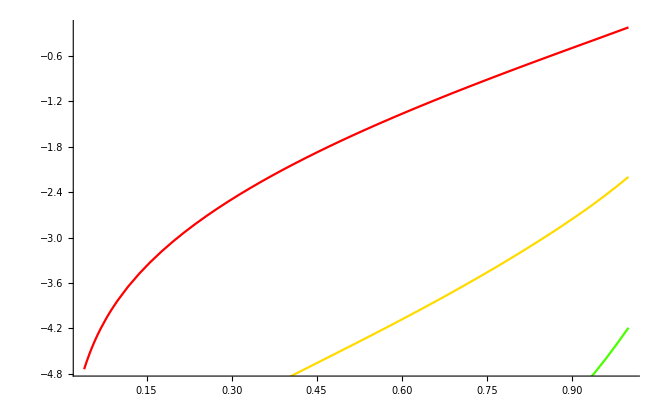

```mathematica
fWhiteFurnace=Table[ListInterpolation[taWhiteFurnace[[order-1]],{0.04,1}],{order,2,countOrders}];
Show[Table[Plot[fWhiteFurnace[[order-1]][ρ],{ρ,0.04,1},PlotRange->Full,PlotStyle->Hue[(order-2)/countOrders]],{order,2,countOrders}]]
Show[Table[Plot[Log[fWhiteFurnace[[order-1]][ρ]],{ρ,0.04,1},PlotRange->Full,PlotStyle->Hue[(order-2)/countOrders]],{order,2,countOrders-1}]]
```

Now let’s try and fit each curve with a polynomial of the form f(F_0)=a_n*F_0^n where n is the order:

{0.802132,0.111081,0.0151042,0.00174776,0.000166766,0.0000148001}

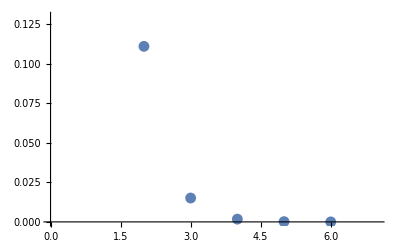

```mathematica
An=Table[fWhiteFurnace[[order-1]][1],{order,2,countOrders}]
ListPlot[An,PlotRange->{{0,7},{0,0.13}}]
```

{0.55744,0.483124,0.481897,0.483984,0.476908}

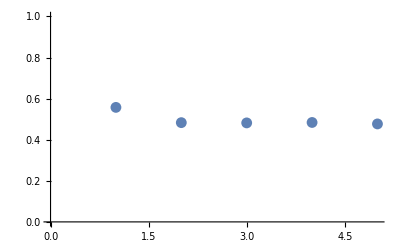

```mathematica
Clear[a,b,c,d,order,x]
fittingMethod="PrincipalAxis";
fittingMethod="LevenbergMarquardt";
fittingMethod="Automatic";

exponent=2;
fitter=Function[{order},
model=An[[order-1]]*x^(a*order^exponent);
data=Table[{ρ,fWhiteFurnace[[order-1]][ρ]},{ρ,0.04,1,0.01}];
fit=FindFit[data,model,{{a,1},{b,0},{c,1},{d,0},e},x,Method->fittingMethod]
];
fits=Table[Function[x,Evaluate[An[[order-1]]*x^(a*order^exponent)/.fitter[order]]],{order,2,countOrders-1}];
fitExponents=Table[a/.fitter[order],{order,2,countOrders-1}]
ListPlot[fitExponents,PlotRange->{0,1}]
```

Great! The exponent factor seems to be 1/2! ^_^

```mathematica
Kn=Table[a/.fitter[order],{order,2,countOrders-1}]
avgK=Sum[a/.fitter[order],{order,2,countOrders-1}]/5
```

{0.55744,0.483124,0.481897,0.483984,0.476908}

0.496671

```mathematica
Manipulate[
Show[
Plot[fWhiteFurnace[[order-1]][ρ],{ρ,0.04,1},PlotRange->{0,fWhiteFurnace[[order-1]][1]},AxesLabel->{"F_0","E_avg"}]
,Plot[fits[[order-1]][ρ],{ρ,0.04,1},PlotStyle->Red,PlotRange->Full]
],{order,2,countOrders-1,1}]
```

So we found an expression of the form:
	f(F_0)=a_n · (√F_0)^(n^2)

Now we will try to make a_n enter this pattern as well by writing:
	a_n=a_1·(√τ)^(n^2)

So that τ can be factored into F_0...

```mathematica
An
```

{0.802132,0.111081,0.0151042,0.00174776,0.000166766,0.0000148001}

{a→3.86558,b→0.4555,c→1.,d→0.,e→1.}

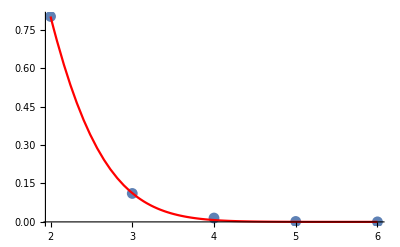

3.86558

0.802031

0.802031

3.86558

0.4555

```mathematica
model=An[[1]]*a*(√b)^(x^2);
model=a*(√b)^(x^2);
data=Table[{order,An[[order-1]]},{order,2,countOrders-1}];
fit=FindFit[data,model,{{a,1},{b,1},{c,1},{d,0},e},x,Method->fittingMethod]
fTau=Function[{x},Evaluate[model/.fit]];
Plot[fTau[x],{x,2,countOrders-1},PlotStyle->Red,PlotRange->Full];
Show[
ListPlot[data,PlotRange->Full]
,Plot[fTau[x],{x,2,countOrders-1},PlotStyle->Red,PlotRange->Full]
]
a2=(a/.fit) (* This can be used to fit experimental data *)
(a/.fit)*(√(b/.fit))^4
3.8655810610440082*(√0.4554998477195002)^4
3.865581061044009
0.45549984771950014
```

So we finally get our final expression:

	a_n(F_0)= a_1 ((F̂)_0)^(n^2)
	(F̂)_0=√(τ · F_0)
	τ=0.45549984771950014
	
We require that:
	∑_(n=2)^∞ a_n(1)=∑_(n=2)^∞ a_1 (√τ)^(n^2)=a_1·∑_(n=2)^∞ (√τ)^(n^2)=1
	
	a_1=1/(∑_(n=2)^∞ (√τ)^(n^2))

The geometric series is computed using the Jacobi elliptic theta 3 function that converges to:

	∑_(n=2)^∞ (√τ)^(n^2)=0.4168994928925871 (numerically computed below)

And so we get:

	a_1 = 1/(∑_(n=2)^∞ (√τ)^(n^2))= 4.193906008161867

```mathematica
τ =0.45549984771950014
Sum[(√τ)^(n^2),{n,2,∞}]
a1=1/Sum[(√τ)^(n^2),{n,2,∞}]
Plot[Sum[(√τ)^(n^2),{n,2,maxN}],{maxN,2,10},PlotRange->Full];
```

0.4555

0.238441

4.19391

```mathematica
4.193906008161867
4.193906008161867
```

4.19391

4.19391

With the “Elliptic Theta” function from Mathematica:
	ϑ_3(u,q)=1+2∑_(n=1)^∞ q^(n^2)cos(2n u)

If we let u=0 then it simplifies into:
	ϑ_3(0,q)=1+2∑_(n=1)^∞ q^(n^2)
	
We are interested in:
	∑_(n=1)^∞ q^(n^2)= (ϑ_3(0,q)-1)/2
	
Furthermore, we are looking for the series starting from n=2 so:

	∑_(n=2)^∞ q^(n^2)=∑_(n=1)^∞ q^(n^2)- q= (ϑ_3(0,q)-1)/2-q= (ϑ_3(0,q)-1-2q)/2

0.674907

0.238441

4.19391

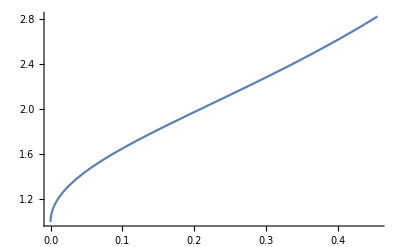

```mathematica
√τ
recA1=(EllipticTheta[3,0, √τ]-1-2 √τ)/2
a1=1/recA1 (* = a1 *)
Plot[EllipticTheta[3,0,√x],{x,0,τ}]
```

```mathematica
4.193906008161867
```

4.19391

We check the final equation sums to 1:

```mathematica
a1
Sum[a1*(√τ)^(n^2),{n,2,countOrders}]
```

4.19391

1.

Same with the elliptic theta:

```mathematica
fEllipticTheta[F0_]:=a1*((EllipticTheta[3,0, √(τ*F0)]-1-2 √(τ*F0))/2)
fEllipticTheta[1]
```

1.

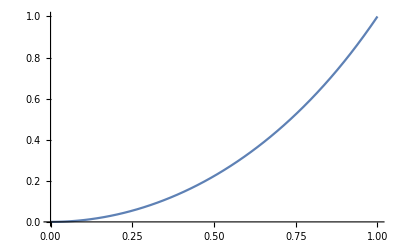

-Graphics-

```mathematica
Plot[Sum[a1*(√(τ*F0))^(n^2),{n,2,100}],{F0,0,1}]
Plot[fEllipticTheta[F0],{F0,0,1},PlotRange->Full]
```

Now we try to fit the elliptic curve with a simple polynomial:

{a→0.,b→0.0393241,c→0.656328,d→0.299557,e→0.}

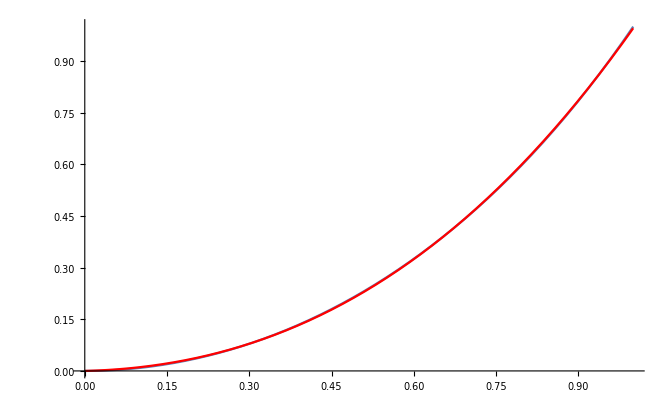

```mathematica
model=0*a+b*x+c*x^2+d*x^3;
data=Table[{F0,fEllipticTheta[F0]},{F0,0,1,0.01}];
fit=FindFit[data,model,{{a,1},{b,1},{c,1},{d,0},e},x,Method->fittingMethod]
fEllipticPoly=Function[{x},Evaluate[model/.fit]];
Plot[fEllipticPoly[x],{x,0,1},PlotStyle->Red,PlotRange->{0,1}];
Show[
Plot[fEllipticTheta[F0],{F0,0,1},PlotRange->{0,1}]
,Plot[fEllipticPoly[F0],{F0,0,1},PlotStyle->Red,PlotRange->Full]
]
```

Final Expression

0.4555

4.19391

1.

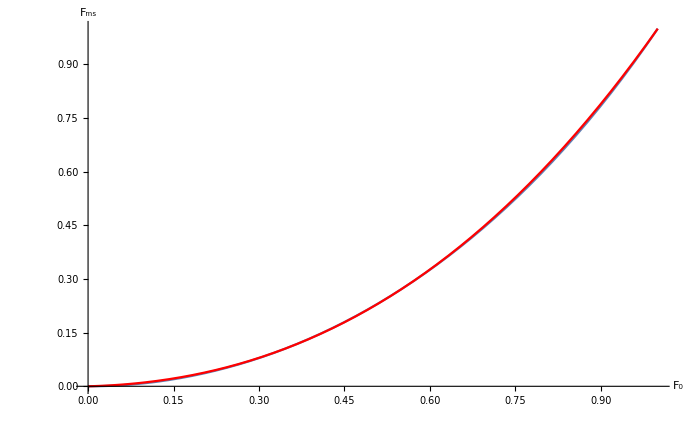

```mathematica
Clear[factorMS]
τ=0.4554998477195002
a1=2/(EllipticTheta[3,0, √τ]-1-2 √τ)
factorMS[F0_]:=F0*(0.039324148543732715+F0*(0.6563284963169776 + F0*0.2995566941543759))
factorMS[F0_]:=F0*(0.04+F0*(0.66+ F0*0.3))
factorMS[1]
Show[
Plot[fEllipticTheta[F0],{F0,0,1},PlotRange->{0,1},AxesLabel->{"F_0","F_ms"}]
,Plot[factorMS[ρ],{ρ,0,1},PlotRange->Full,PlotStyle->Red]
]
```

Verification

Now we must verify that our expression can be substituted to the actual measurements!
We first verify that white furnace results match for each individual orders f_n(F_0) * whiteFurnace[F_0=1] = whiteFurnace[ρ]:

```mathematica
Manipulate[
Show[
Plot[fWhiteFurnace[[order-1]][F0],{F0,0.04,1},PlotRange->{0,1*fWhiteFurnace[[order-1]][1]},AxesLabel->{"F_0","E_avg"}]
,Plot[a2*(√(τ*F0))^(order^2),{F0,0,1},PlotStyle->Red,PlotRange->Full,AxesLabel->{"F_0","E_avg"}]
],{order,2,countOrders-1,1}]
```

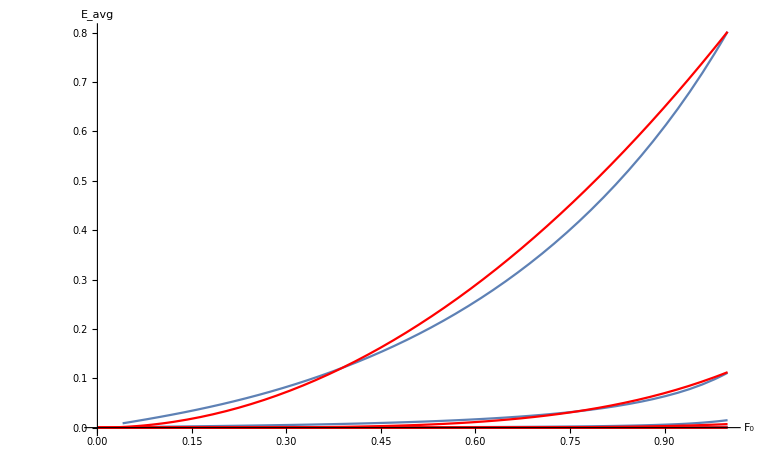

```mathematica
Show[
Table[Plot[fWhiteFurnace[[order-1]][F0],{F0,0.04,1},PlotRange->{0,fWhiteFurnace[[1]][1]},AxesLabel->{"F_0","E_avg"}],{order,2,countOrders-1}]
,Table[Plot[a2*(√(τ*F0))^(order^2),{F0,0,1},PlotStyle->Red,PlotRange->Full],{order,2,countOrders-1}]
]
```

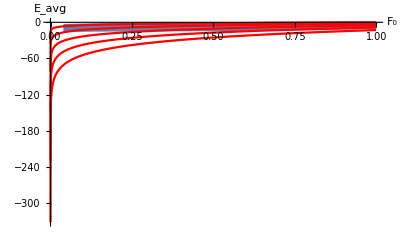

```mathematica
Show[
Table[Plot[Log[fWhiteFurnace[[order-1]][F0]],{F0,0.04,1},PlotRange->{0,-20},AxesLabel->{"F_0","E_avg"}],{order,2,countOrders-1}]
,Table[Plot[Log[a2*(√(τ*F0))^(order^2)],{F0,0,1},PlotStyle->Red,PlotRange->Full],{order,2,countOrders-1}]
]
```

Now we check the sum of all orders:

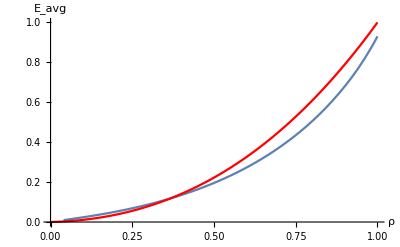

```mathematica
Show[
Plot[Sum[fWhiteFurnace[[order-1]][ρ],{order,2,countOrders-1}],{ρ,0.04,1},PlotRange->{0,1},AxesLabel->{"ρ","E_avg"}]
,Plot[factorMS[ρ],{ρ,0,1},PlotStyle->Red]
]
```

Here we simply check F_0^(n^2/2) dependance:

```mathematica
Manipulate[
Show[
Plot3D[fTotalReflectance[[order]][x,α,F0],{x,0,π/2},{α,0,1},PlotRange->{0,fTotalReflectance[[order]][0.2,1,1]}]
,Plot3D[(√F0)^(order^2)*fTotalReflectance[[order]][x,α,1],{x,0,π/2},{α,0,1},PlotStyle->Red]
],
{{F0,1},0.04,1},{order,2,countOrders-1,1}]
```

# Simulated Multiple-Scattering Diffuse Reflectance Factor

```mathematica
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 
countTheta = 16;
countRoughness= 16;
countAlbedo=20;
countOrders=7;
taRawTotalDiffuseReflectances=Table[
Import["TotalReflectance_Diffuse_Cosine_"  <>ToString[countTheta] <>"x"  <>ToString[countRoughness] <>"x"  <>ToString[countAlbedo] <>"_order"  <>ToString[order] <>".bin", "Real64"],{order,1,countOrders}];
```

Generate list interpolations

```mathematica
fTotalReflectance=Table[
ListInterpolation[Table[
taRawTotalDiffuseReflectances[[order]][[countTheta*((roughness-1)+countRoughness*(albedo-1))+theta]],{theta,1,countTheta},{roughness,1,countRoughness},{albedo,1,countAlbedo}],{{0,π/2},{1,0},{1,0}}],
{order,1,countOrders}];
```

```mathematica
Manipulate[
Plot3D[fTotalReflectance[[order]][x,α,ρ],{x,0,π/2},{α,0,1},PlotRange->{0,3.5^(-order+1)}],{{ρ,1},0,1},{order,1,countOrders,1}]
```

## Show Total Reflectance Depending on Albedo

```mathematica
Manipulate[Plot3D[Sum[fTotalReflectance[[order]][x,α,ρ],{order,1,countOrders}],{x,0,π/2},{α,0,1},PlotRange->{0,1},AxesLabel->{"θ","α"}],{{ρ,1},0,1}]
```

```mathematica
Manipulate[Plot3D[Sum[fTotalReflectance[[order]][x,α,ρ],{order,2,countOrders}],{x,0,π/2},{α,0,1},PlotRange->{0,0.3},AxesLabel->{"θ","α"}],{{ρ,1},0,1}]
```

Visualizing each individual order

```mathematica
Manipulate[
Show[
Table[
Plot3D[fTotalReflectance[[order]][x,α,ρ],{x,0,π/2},{α,0,1},
PlotRange->{0,0.15},PlotStyle->Hue[(4*(order-2))/countOrders]],{order,2,countOrders}]
],
{{ρ,1},0,1}]
```

## White Furnace Comparison

We computed the total energy bouncing off the surface at various scattering orders for different values of roughness, incidence angle and albedos.
So basically we performed:

	E(ω_i,α,ρ)=∫_(Ω^+) L_i(ω_i) f_r( ω_o,ω_i,α,ρ)(ω_o·n)dω_o
	
With L_i(ω_i)=1
To compute the equivalent white furnace test we thus need to compute:

	E_total(α,ρ)=∫_(Ω^+) E(ω_i,α,ρ)(ω_i·n)dω_i

```mathematica
SetDirectory["D:\\Workspaces\\GodComplex\\Tests\\TestMSBRDF\\Tables"]; 
countX=32;
countY=32;
resultOrenEo = Import["MSBRDF_OrenNayar_E32x32.csv","CSV"];
resultOrenEavg = Import["MSBRDF_OrenNayar_Eavg32.csv","CSV"];
fOrenEo=ListInterpolation[Table[resultOrenEo[[1+countX*(y-1)+(x-1)]][[3]],{x,1,countY},{y,1,countY}],{{0,1},{0,1}}]
fOrenEavg=ListInterpolation[Table[resultOrenEavg[[i]][[2]],{i,1,countY}],{0,1}]
Plot[fOrenEavg[x],{x,0,1},PlotRange->{0,π}, AxesLabel->{"α","E_avg"}];
Plot3D[fOrenEo[x,y],{x,0,1},{y,0,1},AxesLabel->{"cos(θ)", "α","E_i"}];

oren=Function[ {θo,ϕo,θi,ϕi,α},
σ=π/2 α;
A = 1-0.5*σ^2/(σ^2+0.33);
B = 0.45*σ^2/(σ^2+0.09);
a=Max[θo,θi];
b=Min[θo,θi];
1/π(A+B*Max[0,Cos[ϕo-ϕi]]*Sin[a]*Tan[b])
];
BRDForen[θo_,θi_,ϕ_,α_]:= oren[θo,0,θi,ϕ,α]
BRDForenms[θo_,θi_,ϕ_,α_]:=((1-fOrenEo[Cos[θo],α])*(1-fOrenEo[Cos[θi],α]))/(π-fOrenEavg[α])
fWhiteFurnaceSS[α_]:=2*π*NIntegrate[BRDForen[θo,θi,ϕi,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
fWhiteFurnaceMS[α_]:=2*π*NIntegrate[BRDForenms[θo,θi,ϕi,α]*Cos[θi]*Sin[θi]*Cos[θo]*Sin[θo],{θi,0,π/2},{ϕi,-π,π},{θo,0,π/2},WorkingPrecision->MachinePrecision]
fWhiteFurnaceSS[0.3]
fWhiteFurnaceMS[0.3]
π-fOrenEavg[0.3]
fWhiteFurnaceSS[0.3]+fWhiteFurnaceMS[0.3]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

InterpolatingFunction[{{0., 1.}}, <>]

2.72499

0.416867

0.416867

3.14186

```mathematica
(*whiteFurnaceMS=Table[{α,fWhiteFurnaceMS[Max[0.01,α]]},{α,0,1,0.05}]*)
```

```mathematica
whiteFurnaceMS=Table[{α,π-fOrenEavg[α]},{α,0,1,0.05}]
```

{{0.,-3.55271×10^-15},{0.05,0.0106767},{0.1,0.0463195},{0.15,0.111741},{0.2,0.203616},{0.25,0.309496},{0.3,0.416867},{0.35,0.518153},{0.4,0.60959},{0.45,0.690019},{0.5,0.759711},{0.55,0.819639},{0.6,0.871008},{0.65,0.915032},{0.7,0.952826},{0.75,0.985365},{0.8,1.01348},{0.85,1.03787},{0.9,1.05912},{0.95,1.07771},{1.,1.09404}}

Here we show that we mustn’t forget that the MS white furnace amounts to the complement of the total energy lost by SS BRDF...

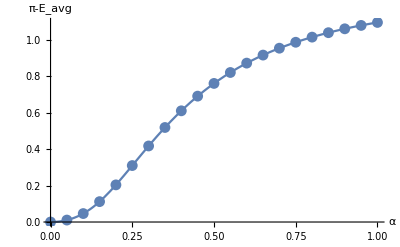

```mathematica
Show[ListPlot[whiteFurnaceMS,PlotRange->Full, AxesLabel->{"α","π-E_avg"}],
Plot[π-fOrenEavg[x],{x,0,1}]
]
```

Comparing with Simulation

We computed the total energy bouncing off the surface at various scattering orders for different values of roughness, incidence angle and albedos.
So basically we performed:

	E(ω_i,α,ρ)=∫_(Ω^+) L_i(ω_i) f_r( ω_o,ω_i,α,ρ)(ω_o·n)dω_o
	
With L_i(ω_i)=1
To compute the equivalent white furnace test we thus need to compute:

	E_total(α,ρ)=∫_(Ω^+) E(ω_i,α,ρ)(ω_i·n)dω_i

```mathematica
taRawSumTotalReflectances=Sum[taRawTotalDiffuseReflectances[[order]],{order,2,countOrders}]; (* Sum all orders > 2 *)
MSTotalReflectances=ListInterpolation[Table[taRawSumTotalReflectances[[countTheta*((roughness-1)+countRoughness*(ρ-1))+theta]],{theta,1,countTheta},{roughness,1,countRoughness},{ρ,1,countAlbedo}],{{0,π/2},{1,0},{1,0}}]
fWhiteFurnaceSimul[α_,ρ_,order_]:=2*π*NIntegrate[fTotalReflectance[[order]][θi,α,ρ]*Cos[θi]*Sin[θi],{θi,0,π/2},WorkingPrecision->MachinePrecision];
fSumWhiteFurnaceSimul[α_,ρ_]:=2*π*NIntegrate[MSTotalReflectances[θi,α,ρ]*Cos[θi]*Sin[θi],{θi,0,π/2},WorkingPrecision->MachinePrecision];
fWhiteFurnaceSimul[1,1,2]
fSumWhiteFurnaceSimul[1,1]
```

InterpolatingFunction[{{0., 1.5708}, {0., 1.}, {0., 1.}}, <>]

0.496629

0.701024

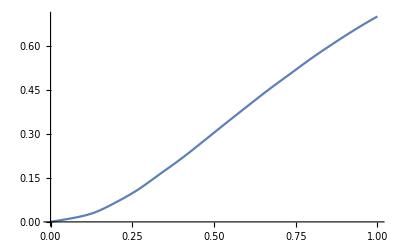

```mathematica
θ=0;
ρ=1;
Plot[fSumWhiteFurnaceSimul[α,ρ],{α,0,1}]
```

```mathematica
factor=1.0940380117056643/fSumWhiteFurnaceSimul[1,1]
```

1.56063

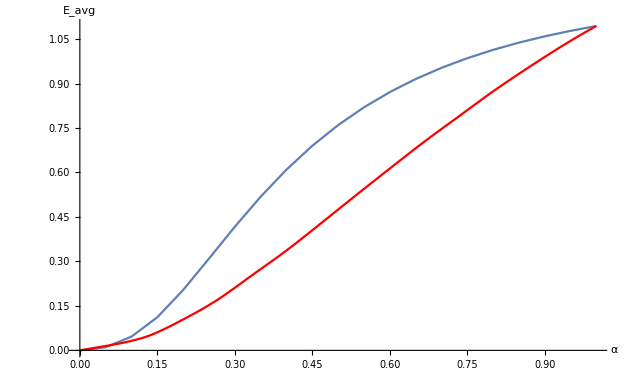

```mathematica
Show[
ListLinePlot[whiteFurnaceMS,AxesLabel->{"α","E_avg"}]
,Plot[factor*fSumWhiteFurnaceSimul[α,ρ],{α,0,1},PlotStyle->Red]
]
```

We see here the red curve is not exactly identical to the white furnace result given by the theoretical multiple-scattering expression for the Oren-Nayar BRDF. Maybe it’s due to the many simplifications of the Oren-Nayar model? Maybe there’s a bias in my simulation?
Overall, we won’t linger too much on these differences and assume the simulation represents ground-truth data.

## Finding an Analytical Model

We saw that integrating our order 2^+ irradiance values (the green curve in the above graph) yields π-E_total where E_total(α,ρ) is the total irradiance reflected for the single-scattering Oren-Nayar BRDF.

We are interested in how each order contributes to that complement.
We assume the roughness-dependent shape is not important and concentrate on the maximum values of the white furnace functions for each order, when α=1. But we are interested in the evolution of that maximum value when varying the albedo.

So let’s create a table of samples of white furnace values for varying albedos, for each order (except last order, which is a compound of all remaining orders and doesn’t interest us):

```mathematica
α=1;
taWhiteFurnaceDiffuse=
Table[fWhiteFurnaceSimul[α,ρ,order],{order,2,countOrders},{ρ,0,1,0.02}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

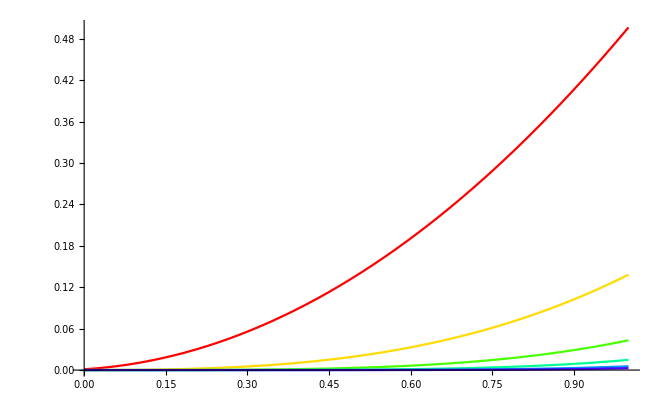

```mathematica
fWhiteFurnaceDiffuse=Table[ListInterpolation[taWhiteFurnaceDiffuse[[order-1]],{0,1}],{order,2,countOrders}];
Show[Table[Plot[fWhiteFurnaceDiffuse[[order-1]][ρ],{ρ,0,1},PlotRange->Full,PlotStyle->Hue[(order-2)/countOrders]],{order,2,countOrders}]]
```

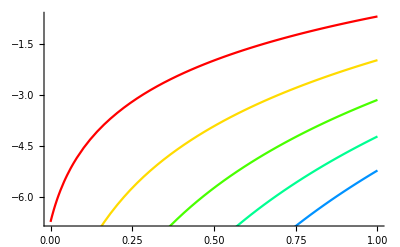

```mathematica
Show[Table[Plot[Log[fWhiteFurnaceDiffuse[[order-1]][ρ]],{ρ,0,1},PlotRange->Full,PlotStyle->Hue[(order-2)/countOrders]],{order,2,countOrders-1}]]
```

Now let’s try and fit each curve with a polynomial of the form f(ρ)=a_n*ρ^n where n is the order:

```mathematica
Clear[a,b,c,d,x]
fittingMethod="LevenbergMarquardt";
fittingMethod="PrincipalAxis";
fittingMethod="Automatic";

fitter=Function[{order},
model=a*x^order;
data=Table[{ρ,fWhiteFurnaceDiffuse[[order-1]][ρ]},{ρ,0,1,0.01}];
fit=FindFit[data,model,{a,b,c,d,e},x,Method->fittingMethod];
Function[x,Evaluate[model/.fit]];
a/.fit
];

fitter[3];
```

```mathematica
values=Table[fitter[order],{order,2,countOrders}]
```

{0.508918,0.141632,0.0442183,0.0151468,0.00559481,0.0028015}

```mathematica
maxValues=Table[fWhiteFurnaceDiffuse[[order-1]][1],{order,2,countOrders}]
```

{0.496629,0.138236,0.0431674,0.0147899,0.0054642,0.00273668}

```mathematica
Manipulate[
Show[
Plot[fWhiteFurnaceDiffuse[[order-1]][ρ],{ρ,0,1},PlotRange->{0,fWhiteFurnaceDiffuse[[order-1]][1]},AxesLabel->{"ρ","E_avg"}]
,Plot[values[[order-1]]*ρ^order,{ρ,0,1},PlotStyle->Red]
,Plot[maxValues[[order-1]]*ρ^order,{ρ,0,1},PlotStyle->Green]
],{order,2,countOrders-1,1}]
```

Since our goal is to make the sum of these values be 1 (since they will guide the factor for the MSBRDF), we compute a normalization factor

```mathematica
limitValue=Sum[whiteFurnaceSimul[1,1,order],{order,2,countOrders}] (* Accurate but won't help *)
limitValue=Sum[maxValues[[i-1]],{i,2,countOrders}] (* We need to use our maximum values instead *)
```

whiteFurnaceSimul[1,1,2]+whiteFurnaceSimul[1,1,3]+whiteFurnaceSimul[1,1,4]+whiteFurnaceSimul[1,1,5]+whiteFurnaceSimul[1,1,6]+whiteFurnaceSimul[1,1,7]

0.701024

{0.725964,0.202036,0.0630767,0.0216066,0.00798091,0.0039963}

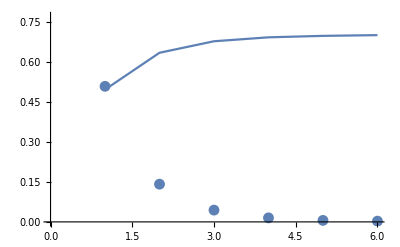

0.701024

```mathematica
newValues=values/limitValue
Show[
ListPlot[values,PlotRange->{0,1.1*limitValue}]
,ListLinePlot[Table[Sum[maxValues[[i]],{i,1,j}],{j,1,countOrders-1}],PlotRange->{0,1.1}](* Show that the sum converges to 1 *)
]
Sum[maxValues[[i-1]],{i,2,countOrders}]
```

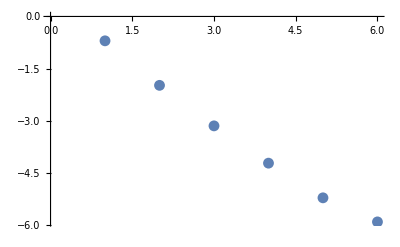

```mathematica
ListPlot[Log[maxValues],PlotRange->Full]
```

Now we can see the graph of amplitudes for each order is clearly a geometric progression, as expected.
We’re looking for a function of the type:

	f_n(ρ)=a_1 (τρ)^n

We already isolated the ρ^n part, now we’re looking for the terms a_1 and τ so that a_1·τ^n follows our table of values computed for ρ=1;

{a→6.13852,b→0.284304,c→1.,d→1.,e→1.}

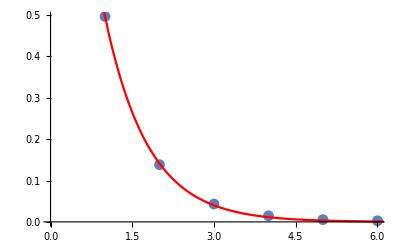

```mathematica
model=a*b^(x+1);(* We need a geometric progression, x+1 because x=1 is actually order 2! *)
data=maxValues;
fit=FindFit[data,model,{a,b,c,d,e},x,Method->fittingMethod]
ffit=Function[x,Evaluate[model/.fit]];
Show[
ListPlot[maxValues,PlotRange->Full],
Plot[ffit[x],{x,0.1,countOrders},PlotStyle->Red]
]
```

We have our τ factor:

	f_n(ρ)= a_1 (τρ)^n
	τ=0.28430405702379613


Since ρ<=1 then τρ<1 and we have a well-behaved geometric series that can be simplified into the final expression:

	∑_(n=2)^∞ (τρ)^n=(τρ)^2/(1 - τρ)
	
The total amplitude for multiply-scattered energy should be:

	∑_(n=2)^∞ f_n(1) =1
	
And so:
	∑_(n=2)^∞ a_1 τ^n = a_1 ∑_(n=2)^∞ τ^n= a_1 τ^2/(1 - τ)=1

And simply:

	a_1 =(1 - τ)/τ^2

6.13852

0.284304

8.85447

1.

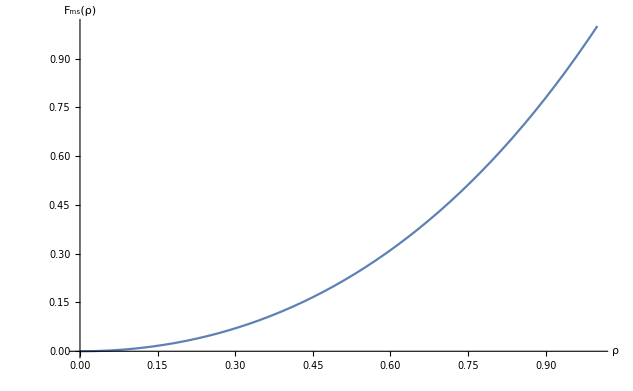

```mathematica
Clear[factorMS]
a1=a/.fit
τ=b/.fit
a2=(1-τ)/τ^2
factorMS[ρ_]:=a2*(τ*ρ)^2/(1-τ*ρ)
factorMS[1]
Plot[factorMS[ρ],{ρ,0,1},PlotRange->All,AxesLabel->{"ρ","F_ms(ρ)"}]
```

Verification

Now we must verify that our expression can be substituted to the actual measurements!
We first verify that white furnace results match for each individual orders f_n(ρ) * whiteFurnace[ρ=1] = whiteFurnace[ρ]:

```mathematica
Manipulate[
Show[
Plot[fWhiteFurnaceDiffuse[[order-1]][ρ],{ρ,0,1},PlotRange->{0,fWhiteFurnaceDiffuse[[order-1]][1]},AxesLabel->{"ρ","E_avg"}]
,Plot[a1*(τ*ρ)^order,{ρ,0,1},PlotStyle->Red]
],{order,2,countOrders-1,1}]
```

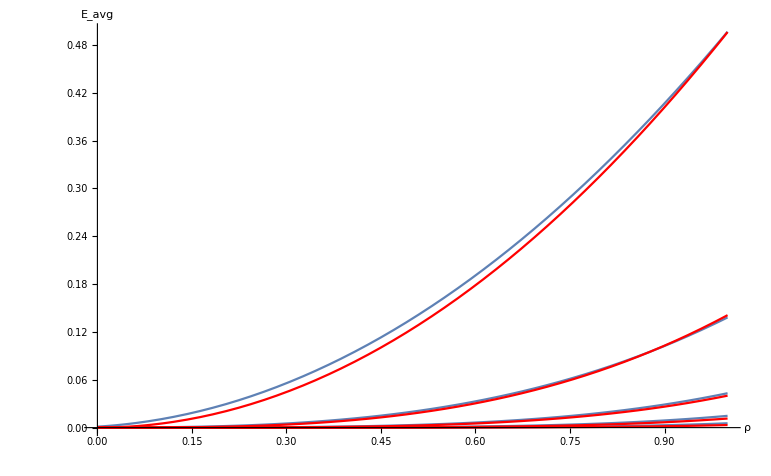

```mathematica
Show[
Table[Plot[fWhiteFurnaceDiffuse[[order-1]][ρ],{ρ,0,1},PlotRange->{0,fWhiteFurnaceDiffuse[[1]][1]},AxesLabel->{"ρ","E_avg"}],{order,2,countOrders-1}]
,Table[Plot[a1*(τ*ρ)^order,{ρ,0,1},PlotStyle->Red,PlotRange->Full],{order,2,countOrders-1}]
]
```

Now we check the sum of all orders:

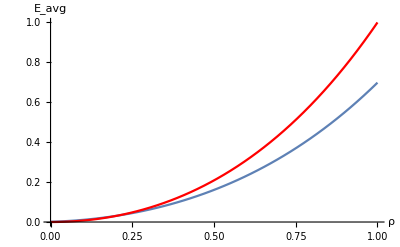

```mathematica
Show[
Plot[Sum[fWhiteFurnaceDiffuse[[order-1]][ρ],{order,2,countOrders-1}],{ρ,0,1},PlotRange->{0,1},AxesLabel->{"ρ","E_avg"}]
,Plot[factorMS[ρ],{ρ,0,1},PlotStyle->Red]
]
```

Here we simply check ρ^n dependence:

```mathematica
Manipulate[
Show[
Plot3D[fTotalReflectance[[order]][x,α,albedo],{x,0,π/2},{α,0,1},PlotRange->{0,fTotalReflectance[[order]][0.2,1,1]}]
,Plot3D[albedo^order*fTotalReflectance[[order]][x,α,1],{x,0,π/2},{α,0,1},PlotStyle->Red]
],
{{albedo,1},0,1},{order,2,countOrders-1,1}]
```